MAD 4401 Computer Project 1
9/23/2019
Group 8 - Mical Estifanos, Johnny Li, Shawn Hatchwell, Trevor Vente

The problems were individually completely solved by the respective student. 

Problem #1 -by Mical Estifanos

```mathematica
P1 =Normal[Series[Exp[-x^2], {x, 0, 1}]]
```

1

```mathematica
P5 =Normal[Series[Exp[-x^2], {x, 0, 5}]]
```

1-x^2+x^4/2

```mathematica
P10 = Normal[Series[Exp[-x^2], {x, 0, 10}]]
```

1-x^2+x^4/2-x^6/6+x^8/24-x^10/120

```mathematica
f[x] = Exp[-x^2]
```

ⅇ^(-x^2)

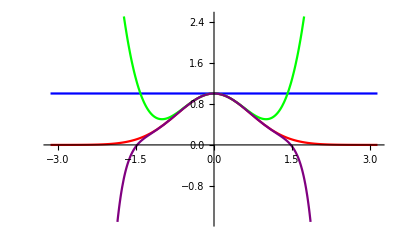

```mathematica
Plot[{f[x], P1, P5, P10}, {x, -Pi, Pi}, PlotStyle->{Red, Blue, Green, Purple}]
```

Problem #2 -by Mical Estifanos

WolframAlphaQueryParseResults

{x→-0.0835599}

**FindRoot finds one solution, NSolve finds all solutions of the system**

WolframAlphaQueryResults

x≈-0.0835599

WolframAlphaQueryParseResults

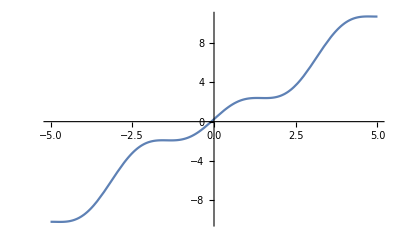

Problem #3 -by Johnny Li

Find the number of iterations :
  | p_n-p|≤((b-a)/2^n) < tolerance

```mathematica
a0=-1;(*Interval range[-1,0]*)
b0=0;
solve[(b0-a0)/2^n<10^-5,{n},integers]
```

solve[True,{17},integers]

```mathematica
f[x_]=2*x*Cos[2*x]-(x+1)^2;    (*function*)
(*Initial look at function*)
```

```mathematica
Plot[{f[x_], 2*x*Cos[2*x] - (x + 1)^2}, {x, -1, 0}]
```

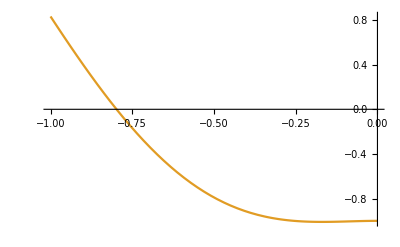

Bisection Method Algorithm

```mathematica
f[x_]=2*x*Cos[2.*x]-(x+1)^2;  (*function*)

(*Initial Check to see if the function can be solved with 
the bisection method.*)
a=-1;   (*Interval range[-1,0]*) 
b=0;
If[f[a]*f[b]>0,{Print["No solution exists"] Exit[]}];

(*Function can be solved with the Bisection Method, start by 
the given interval range.*)
n=17;    (*number of iteration*)
tol=10^-5;    (*tolerance*)
Print["n   a   b   c  f(c) tolerance"];
(*Loop for root*)
For[i=0,i<n,i++,
If[f[a]*f[b]<0,{   (*check for opposite sign*)
c=(b+a)/2.;     (*get the c value*)
	If[f[a]*f[c]<0, (*check for opposite sign for [a,c]*)
		Print[{i,a,b,c,f[c],tol}];
		b=c];    (*Let c be b*)
	If[f[b]*f[c]<0, (*check for opposite sign for [b,c]*)
		Print[{i,a,b,c,f[c],tol}];
		a=c];   (*Let c be a*)
}];
];
Print["Finish"];
```

n   a   b   c  f(c) tolerance

{0,-1,0,-0.5,-0.790302,1/100000}

{1,-1,-0.5,-0.75,-0.168606,1/100000}

{2,-1,-0.75,-0.875,0.296306,1/100000}

{3,-0.875,-0.75,-0.8125,0.0528816,1/100000}

{4,-0.8125,-0.75,-0.78125,-0.0608144,1/100000}

{5,-0.8125,-0.78125,-0.796875,-0.00468056,1/100000}

{6,-0.8125,-0.796875,-0.804688,0.0239252,1/100000}

{7,-0.804688,-0.796875,-0.800781,0.00957807,1/100000}

{8,-0.800781,-0.796875,-0.798828,0.00243764,1/100000}

{9,-0.798828,-0.796875,-0.797852,-0.00112424,1/100000}

{10,-0.798828,-0.797852,-0.79834,0.000656003,1/100000}

{11,-0.79834,-0.797852,-0.798096,-0.000234294,1/100000}

{12,-0.79834,-0.798096,-0.798218,0.000210811,1/100000}

{13,-0.798218,-0.798096,-0.798157,-0.0000117525,1/100000}

{14,-0.798218,-0.798157,-0.798187,0.0000995265,1/100000}

{15,-0.798187,-0.798157,-0.798172,0.0000438863,1/100000}

{16,-0.798172,-0.798157,-0.798164,0.0000160667,1/100000}

Finish

Problem #4 -by Trevor Vente

```mathematica
RegFalsi[a0_,b0_]:=Module[{},a=N[a0];b=N[b0];c=(a*f[b]-b*f[a])/(f[b]-f[a]);n=0;
output={{n,a,c,b,f[c]}};
root = x /. FindRoot[f[x], {x,c}];
Print["root - c = ",Abs[root-c]];
While[Abs[root-c] > 10^-5, If[Sign[f[b]]==Sign[f[c]],b=c,a=c;];
c=(a*f[b]-b*f[a])/(f[b]-f[a]);
n=n+1;
output=Append[output,{n,a,c,b,f[c]}];];
Print[NumberForm[TableForm[output,TableHeadings->{None,{"n","a","c","b","f[c]"}}],16]];
Print[" root = ", root];
Print[" c = ",NumberForm[c,16]];
Print[" f[c] = ",NumberForm[f[c],16]];]
f[x_]=2*x*Cos[2*x]-(x+1)^2
```

-(1+x)^2+2 x Cos[2 x]

```mathematica
RegFalsi[-1, 0]
```

root - c = 0.252396

n | a | c | b | f[c]
0 | -1. | -0.5457640413674794 | 0. | -0.7096666379850487
1 | -1. | -0.7548200743265998 | -0.5457640413674794 | -0.1523794788574126
2 | -1. | -0.7927619936592848 | -0.7548200743265998 | -0.01959737638184232
3 | -1. | -0.7975294122316234 | -0.7927619936592848 | -0.002298024714702703
4 | -1. | -0.7980869092878649 | -0.7975294122316234 | -0.0002663559539167124
5 | -1. | -0.7981515061361502 | -0.7980869092878649 | -0.00003083042463096486

root = -0.79816

c = -0.7981515061361502

f[c] = -0.00003083042463096486

Problem #5 -by Shawn Hatchwell

“A function f(x) is to be computed at N equally spaced points x1, x2, x3,  . . . , xn, where N is large. Two algorithms to accomplish this task are provided below, each described in pseudocode. Explain why both algorithms produce the same results if exact arithmetic is used. Which of the two algorithms would you prefer to use on a computer device, using machine arithmetic? Give reasons for your choice. Code an example in Mathematica, where the two algorithms differ.”

Both algorithms are trying to find the value of xi = i*1/N and f(xi) for each value of i up to N. Algorithm 1 attempts to do this through means of additions, and Algorithm 2 through means of multiplication. With exact arithmetic the two are equivalent at each step because, for an arbitrary step n,

∑_(i=1)^n 1/N=1/N+1/N+...+1/N= n(1/N),

where the summation on the left is representative of Algorithm 1 and the product on the right is representative of Algorithm 2. Since the algorithms end after N steps, the algorithms will evaluate to N*(1/N)=1.
On the other hand, with machine arithmetic, the algorithms differ greatly. To get to a given step in Algorithm 1, the results of each step before it matters, since they are all added onto each other. This means that a small error in the initial value of 1/N will be stretched out over multiple steps. A given step in Algorithm 2, however, is independent from the previous steps, since only one multiplication is done as opposed to numerous additions, meaning that the error will likely be much smaller.

Computed Value: 0. Alg1: {{1.01,0.00995033}} Alg2: {{1.,0.}}

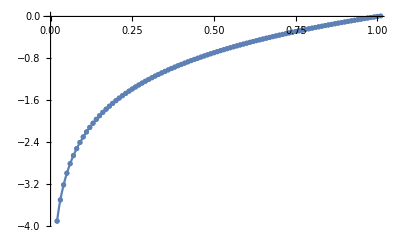

```mathematica
Alg1[N_,f_]:=Module[{x,h,l},
x=0;
h=1/N;
l=List[];
For[i=0,i<=N,i++,
x=x+h;
y=f[x];
AppendTo[l,{x,y}];
];
Return[l];
]
Alg2[N_,f_]:=Module[{x,h,l},
x=0;
h=1/N;
l=List[];
For[i=0,i<=N,i++,
x=i*h;
y=f[x];
AppendTo[l,{x,y}];
];
Return[l];
]
Compare[N_,f_]:=Module[{l1,l2},
l1=Alg1[N,f];
l2=Alg2[N,f];
Print["Computed Value: ",f[1.]," Alg1: ",l1[[-1;;]]," Alg2: ",l2[[-1;;]]];
Show[
Plot[f[x],{x,0,1}],
ListPlot[l1],
ListPlot[l2]
]
]
Compare[100.,Log]
```